```mathematica
(*velocidad media de precesión*)
datafrecond1={{0.2115,0.00268},{0.1905,0.314},{0.1705,0.663},{0.1505,0.989},{0.1305,1.29},{0.1105,1.64}};
(*l es la l2 al cuadrado*)
datafit1=NonlinearModelFit[datafrecond1,{l*a+b},{a,b},l]
datafit1[{"BestFit","ParameterTable"}]
```

FittedModel[3.42346-16.2262 l]

{3.42346-16.2262 l, | Estimate | Standard Error | t-Statistic | P-Value
a | -16.2262 | 0.177967 | -91.1754 | 8.67545×10^-8
b | 3.42346 | 0.0292415 | 117.075 | 3.1921×10^-8}

```mathematica
graph1=Plot[datafit1[l],{l,0.1,0.25},PlotLegends->{"Velocidad media de precesión"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0.1,0.22},{-0.1,2}},Frame->True,FrameLabel->{Style["l₂ / m ",Bold,16],Style[" ϕ ̇ / rad s⁻.b9",16,Bold]}];
Needs["ErrorBarPlots`"];
```

```mathematica
pplot1=ListPlot[datafrecond1 ,PlotStyle->{Black,Thickness[0.003]},PlotLegends -> {"Datos experimentales"}];
dataerr1=ErrorListPlot[{{{0.2115,0.00268},ErrorBar[0.001118034,0.00022]},{{0.1905,0.314},ErrorBar[0.00111803,0.0019]},{{0.1705,0.663},ErrorBar[0.00111803,0.0052]},{{0.1505,0.989},ErrorBar[0.00111803,0.015]},{{0.1305,1.29},ErrorBar[0.00111803,0.023]},{{0.1105,1.64},ErrorBar[ 0.00111803 ,0.045]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

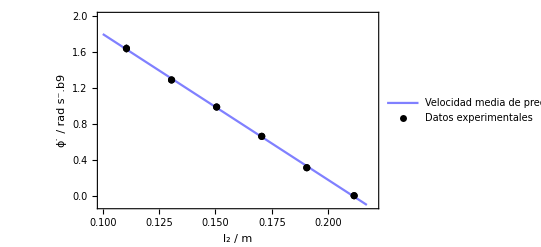

```mathematica
Show[graph1,pplot1,dataerr1]
```